# Characteristic Function

Consider a Markov chain, where with the probability 1/ⅇ generates a new random value ξ_i and otherwise ticks a time. Then the number of generated values per time tick is geometrically distributed: (1-ⅇ)ⅇ^m. Take λ:=-m/x where x:=∑_(i=1)^m ξ_i. Then for fixed x, λ x is also geometrically distributed.

Let’s try to find a physical sense for characteristic functions. Take some distribution:

```mathematica
distr = PoissonDistribution[1/3]
```

PoissonDistribution[1/3]

```mathematica
PoissonDistribution[1/3]
```

```mathematica
PoissonDistribution[3]
```

PoissonDistribution[3]

9.

Generate a chunk of random numbers with this distribution. Each row contains geometrically-distributed number of random numbers with parameter p, other numbers in the row are zeroes.

```mathematica
getChunk[distr_,size_,p_]:=Module[{lengths=Min[size,#]&/@RandomVariate[GeometricDistribution[p],size]},
{RandomVariate[distr,{size,size}]*(Join[ConstantArray[1,#],ConstantArray[0,size-#]]&/@lengths), lengths}]
```

```mathematica
chunk=getChunk[distr,1000, 0.24];
Mean[Total[chunk[[1]],{2}]]
Mean[If[#[[2]]==0,0,Total[#[[1]]]/#[[2]]]&/@(Transpose@chunk)]>1;
```

999/1000

Ideally, in each row we have many variates (so p should be relatively small) and some filled zeroes (so the size of list should be large). Let’s calculate the list size. Take some δ and p=1/δ (in this case only δ of all rows will have zero variates) For this p find inverse CDF in the point in the point 1-δ:

```mathematica
listSize[δ_]:=n/.FindInstance[CDF[GeometricDistribution[δ],n]>1-δ,n, Integers][[1]]
listSize[.001]
```

6964

```mathematica
δ=.005
size=listSize[δ]
```

0.005

1172

```mathematica
0.0001
```

6964

Calculate for each chunk average speed and average number of steps:

```mathematica
aggChunk[distr_,size_,p_]:=Module[{chunk=getChunk[distr,size,p]},{Total[chunk[[1]],{2}],chunk[[2]]}]
```

```mathematica
data=aggChunk[distr,size,.24];
```

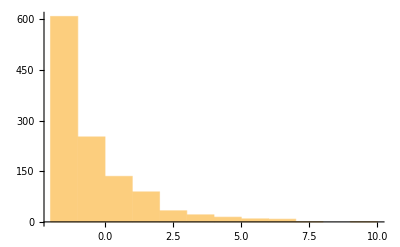

```mathematica
Histogram[data[[1]]-Mean[data[[1]]]]
```

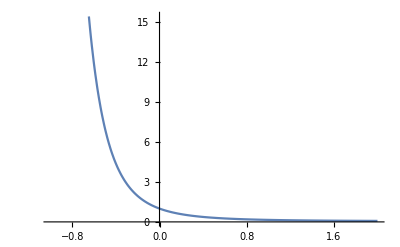

```mathematica
Plot[ⅇ^(3(ⅇ^-t-1)),{t,-1,2}]
```